电势与电场表达式构建完成。

【核心结果】总电势 phi(x,y,z) 的表达式:

-2/(√(x^2+y^2+(z-1)^2))+1/(√((x-1)^2+y^2+z^2))+1/(√((x+1)^2+y^2+z^2))

正在寻找平衡点...

找到的平衡点坐标 (清洗后): {{0,0,-0.620721}}

--------------------

正在分析点: {0,0,-0.620721}

特征值: {-1.89957,1.14272,0.756847}

结论: 不稳定 (Unstable)

生成可视化图表...

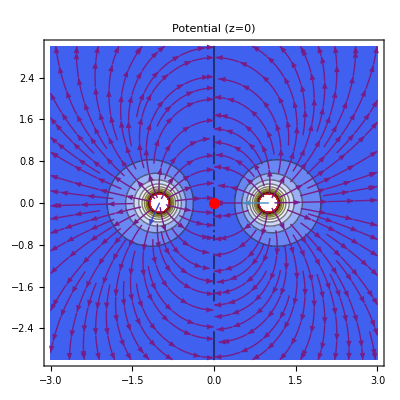

```mathematica
(* ==========================================*)(*M1 Task 2:静电场完整解决方案 (最终修复版)*)(* ==========================================*)(*---2.1 定义物理模型---*)(*这里的结构是 {电荷量,{x,y,z}}*)charges={{1,{1,0,0}},{1,{-1,0,0}},{-2,{0,0,1}}};

dist[r_List,r0_List]:=Norm[r-r0];

(*定义电势 phi*)
(*修复记录：放弃复杂的 iterator 写法，改用基础下标遍历*)
p={x,y,z};
phi[x_,y_,z_]=Sum[charges[[i,1]]/dist[p,charges[[i,2]]],{i,1,Length[charges]}];

(*计算电场 E=-Grad(phi)*)
fieldE=-Grad[phi[x,y,z],p];
Print["电势与电场表达式构建完成。"];

(*---修正 1:重新定义距离函数---*)(*之前的 Norm 会导致求导出现 Abs'，改用代数写法 Sqrt*)(*这样 Grad 出来的结果就是纯净的代数式，没有 weird artifacts*)dist[r_List,r0_List]:=Sqrt[(r[[1]]-r0[[1]])^2+(r[[2]]-r0[[2]])^2+(r[[3]]-r0[[3]])^2];

(*重新构建电势和电场 (必须重新运行这一段)*)
p={x,y,z};
phi[x_,y_,z_]=Sum[charges[[i,1]]/dist[p,charges[[i,2]]],{i,1,Length[charges]}];
fieldE=-Grad[phi[x,y,z],p];
Print["【核心结果】总电势 phi(x,y,z) 的表达式:"];
(*使用 TraditionalForm 输出漂亮的数学格式，方便你抄写*)
Print[TraditionalForm[phiExpr]];

(*---修正 2:寻找平衡点---*)
Print["正在寻找平衡点..."];

(*计算 z 轴上的场*)
EzOnAxis=fieldE[[3]]/. {x->0,y->0};

(*求解，并使用 Normal 去除 ConditionalExpression*)
(*这是一个关键技巧：Normal 可以把 "x -> 3 if x>0" 变成简单的 "x -> 3"*)
solZ=Normal[NSolve[EzOnAxis==0&&-2<z<2,z,Reals]];

(*构造 3D 点*)
zeros=Table[{0,0,z}/. s,{s,solZ}];
Print["找到的平衡点坐标 (清洗后): ",zeros];

(*---修正 3:稳定性分析---*)
(*计算雅可比矩阵*)
jacobian=Grad[fieldE,{x,y,z}];

Do[pt=zeros[[i]];
Print["\n--------------------"];
Print["正在分析点: ",pt];
(*技巧:先把坐标代进去变成纯数字矩阵，再求特征值*)(*避免带着 x,y,z 符号求特征值，那样算不动*)numJacobian=jacobian/. {x->pt[[1]],y->pt[[2]],z->pt[[3]]};
(*N[...] 强制转为小数*)evals=Eigenvalues[N[numJacobian]];
Print["特征值: ",evals];
If[Max[Re[evals]]>0,Print["结论: 不稳定 (Unstable)"],Print["结论: 稳定 (Stable)"]];,{i,1,Length[zeros]}];

(*---2.4 可视化---*)
(*修复记录：加入 PlotRange 解决电势无穷大导致的空白问题*)
contour=ContourPlot[phi[x,y,0],{x,-3,3},{y,-3,3},Contours->20,ColorFunction->"TemperatureMap",PlotRange->{-5,5},PlotLabel->"Potential (z=0)",Epilog->{Red,PointSize[0.02],Point[{0,0}]}];

stream=StreamPlot[fieldE[[1;;2]]/. z->0,{x,-3,3},{y,-3,3},StreamColorFunction->"Rainbow"];

Print["\n生成可视化图表..."];
Show[contour,stream]
```

验证点的 z 坐标: -0.620721

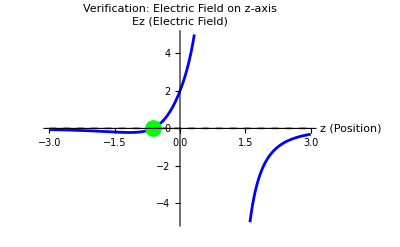

```mathematica
(* ==========================================*)(*结果自查：绘制 z 轴上的电场分布 (修复版)*)(* ==========================================*)(*1. 重新定义绘图函数 (防止前面没运行)*)EzFunction[z_]=Simplify[fieldE[[3]]/. {x->0,y->0}];

plotCheck=Plot[EzFunction[z],{z,-3,3},PlotRange->{-5,5},Exclusions->{1},PlotStyle->{Blue,Thickness[0.005]},AxesLabel->{"z (Position)","Ez (Electric Field)"},GridLines->{{},{0}},GridLinesStyle->Directive[Red,Dashed],PlotLabel->"Verification: Electric Field on z-axis"];

(*2. 标记点 (关键修复)*)
(*先提取出 z 的数值，避免括号混乱*)
(*zeros[[1]] 是第一个解 {0,0,z}，zeros[[1,3]] 就是那个 z 值*)
zVal=zeros[[1,3]];

Print["验证点的 z 坐标: ",zVal];

(*注意：Point[{x,y}] 必须有大括号包围坐标对*)
(*强制显示红线和绿点*)Show[plotCheck,Graphics[{Red,Dashed,Thickness[0.003],Line[{{-3,0},{3,0}}],(*手动画红虚线*)Green,PointSize[0.03],Point[{zVal,0}] (*绿点*)}]]
```